# Condiciones de regularidad alfa-beta

```mathematica
ff3:=PowerExpand[Simplify[-(-7 r^2 α-36 β)/(36 β)-(-49 r^4 α^2+756 r^4 β)/(18 2^(2/3) β (686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2+√(4 (-49 r^4 α^2+756 r^4 β)^3+(686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2)^2))^(1/3))+1/(36 2^(1/3) β)(686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2+√(4 (-49 r^4 α^2+756 r^4 β)^3+(686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2)^2))^(1/3)],Assumptions->{α>0,β>0,r>0}]
```

### Tendencia de f(r) en la región asintótica

```mathematica
FullSimplify[Assuming[α>0&&β>0&&r>0,Simplify[Series[ff3,{r,Infinity,2}]]]]
```

((7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3)) r^2)/(36 β)+1+((c+α) (-1134 α^2 β+23328 β^2+7 √21 α^3 √(-7 α^2+144 β)-162 √21 α β √(-7 α^2+144 β)) (-7 7^(2/3) α^2+108 7^(2/3) β+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))/(9 (7 α^2-144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) r^2)+O[1/r]^3

```mathematica
Simplify[Solve[((c+α) (7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))/(9 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3))==-μ,c]]
```

{{c→-α-(9 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))}}

```mathematica
c:=-α-(9 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))
```

```mathematica
FullSimplify[Assuming[α>0&&β>0&&r>0,Simplify[Series[ff3,{r,Infinity,2}]]]]
```

((7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3)) r^2)/(36 β)+1-μ/r^2+O[1/r]^3

### Región asintóticamente plana

Less::nord: Invalid comparison with 4.37499-1.22858 ⅈ attempted.

Less::nord: Invalid comparison with 8.71341-1.45562×10^-16 ⅈ attempted.

Less::nord: Invalid comparison with 2.43055-0.987793 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

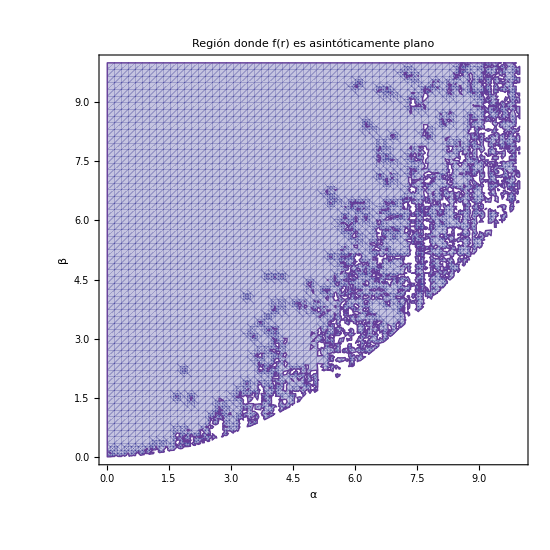

```mathematica
reg=RegionPlot[1/(36 β)(7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))<(10)^(-26),{α,0,10},{β,0,10},PlotPoints->60,Frame->True,FrameStyle->Directive[Black,1.6],FrameTicksStyle->Directive[Black,14],FrameLabel->{Style["α",20,FontFamily->"Times",Bold],Style["β",20,FontFamily->"Times",Bold]},LabelStyle->Directive[16,FontFamily->"Times"],PlotLabel->Style["Región donde f(r) es asintóticamente plano",22,Bold,FontFamily->"Times"],ImageSize->550,PlotTheme->"Classic",BaseStyle->{FontFamily->"Times",16}]
```

```mathematica
curva=Plot[7*(α^2)/108,{α,0,10},PlotStyle->{Red,Thick}];
curvalit=Plot[108*(α^2)/108,{α,0,10},PlotStyle->{Black,Thick}];
curva2=Plot[7*(α^2)/144,{α,0,10},PlotStyle->{Blue,Thick}];
curva3=Plot[7*(α^2)/162,{α,0,10},PlotStyle->{Orange,Thick}];
```

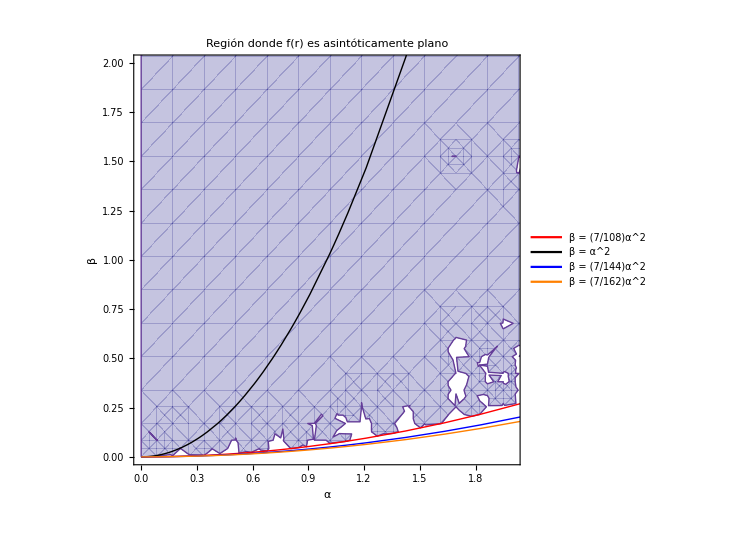

```mathematica
regajus=Legended[Show[reg,curva,curvalit,curva2,curva3,PlotRange->{{0,2},{0,2}}],Placed[LineLegend[{Red,Black,Blue,Orange},{Style["β = (7/108)α^2",16,FontFamily->"Times"],Style["β = α^2",16,FontFamily->"Times"],Style["β = (7/144)α^2",16,FontFamily->"Times"],Style["β = (7/162)α^2",16,FontFamily->"Times"]},LegendFunction->Framed,Spacings->1.2],Right]]
```

```mathematica
Export["Restriccion de beta para asintitocamente plano.png",reg]
```

Restriccion de beta para asintitocamente plano.png

```mathematica
Export["Restriccion mas curvas notables.png",regajus]
```

Restriccion mas curvas notables.png

### ¿Qué ocurre si β<(7/108) α^2?

```mathematica
fmenor=Assuming[α>0&&r>0,FullSimplify[ff3/.β->(1/108)α^2]]
```

1+1/(2 α)3 r^(2/3) (14 r^(4/3)+(12 14^(2/3) r^(8/3))/(154 r^4-(17+√357) α μ+2 7^(1/6) √((-616 7^(1/6) (3 2^(2/3) (-187 ⅈ √7-415 √17) (77+ⅈ √119)^(1/3)+7^(1/6) (10727 ⅈ+2189 √119)) r^4 α μ+34 2^(1/3) (415 ⅈ-11 √119) (77+ⅈ √119)^(2/3) α^2 μ^2-476 ⅈ 2^(2/3) r^8 (-13115878279 (-3401+180 √357)+2521664915 ⅈ )^(1/3))/((-415 ⅈ+11 √119) (-12 7^(1/3)+2^(1/3) (77+ⅈ √119)^(2/3))^2)))^(1/3)+14^(1/3) (154 r^4-(17+√357) α μ+2 7^(1/6) √((-616 7^(1/6) (3 2^(2/3) (-187 ⅈ √7-415 √17) (77+ⅈ √119)^(1/3)+7^(1/6) (10727 ⅈ+2189 √119)) r^4 α μ+34 2^(1/3) (415 ⅈ-11 √119) (77+ⅈ √119)^(2/3) α^2 μ^2-476 ⅈ 2^(2/3) r^8 (-13115878279 (-3401+180 √357)+2521664915 ⅈ )^(1/3))/((-415 ⅈ+11 √119) (-12 7^(1/3)+2^(1/3) (77+ⅈ √119)^(2/3))^2)))^(1/3))

La función se vuelve imaginaria

```mathematica
FullSimplify[Assuming[α>0&&β>0&&r>0,Simplify[Series[ff3,{r,Infinity,2}]]]]
```

((7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3)) r^2)/(36 β)+1-μ/r^2+O[1/r]^3

### Región dentro del agujero negro

```mathematica
serieOriginal=Series[ff3,{r,0,2}];
```

```mathematica
Assuming[α>0&&β>0&&r>0&&c>0,FullSimplify[serieOriginal]]
```

1+(7 α r^2)/(36 β)+O[r]^(7/3)

```mathematica
Assuming[α>0&&β>0&&r>0&&μ>0,FullSimplify[ff3]]
```

1+(7 r^2 α)/(36 β)+(7^(2/3) r^4 (7 α^2-108 β))/(36 β (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3))+1/(36 β)7^(1/3) (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3)

### Reescalado

```mathematica
fsim:=1+(7 r^2 α)/(36 β)+
(7^(2/3) r^4 (7 α^2-108 β))/(36 β (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3))+1/(36 β)7^(1/3) (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3)
```

Construiremos las siguientes funciones

```mathematica
E1:=-7 α^2+144 β
B1:=49 α^3-1134 α β+54 √21 β √E1
D1:=7 √21 α^3-162 √21 α β+162 β √E1
D2:=7^(5/3) α^2-7^(1/3) (108 7^(1/3) β+B1^(2/3))
```

```mathematica
C1:=7 r^6 (7 α^3-162 α β)+((17496 r^2 β^2 √E1 (B1)^(4/3) μ)/((D1) (D2)))+18 √3 r^2 β Sqrt[(-63 r^8 (-E1)+((252 r^4 α (7 α^2-162 β) √E1 (B1)^(4/3) μ)/((D1) (D2)))+(314928 β^2 (E1) (B1)^(8/3) μ^2)/((D1)^2 (D2)^2))]
```

```mathematica
f3sim=1+(7 r^2 α)/(36 β)+(7^(2/3) r^4 (7 α^2-108 β))/(36 β (C1)^(1/3))+1/(36 β)7^(1/3) (C1)^(1/3)
```

1+(7 r^2 α)/(36 β)+(7^(2/3) r^4 (7 α^2-108 β))/(36 β (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3))+1/(36 β)7^(1/3) (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3)

```mathematica
Assuming[α>0&&β>0&&μ>0&&r>0,Simplify[fsim-f3sim]]
```

0

```mathematica
E1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[E1/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
B1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[B1/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
D1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[D1/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
D2rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[D2/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
C1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[C1/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
```

(-7+144 b) α^2

(49+54 b (-21+√21 √(-7+144 b))) α^3

(7 √21-162 b (√21-√(-7+144 b))) α^3

-7^(1/3) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)) α^2

-46656/49 b^3 (-7+162 b) r2^6 α^6+(629856 b^3 √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^2 α^5 μ)/(7 7^(1/3) (-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+69984/49 b^3 r2^2 α^(9/2) √(3888/7 b^2 (-7+144 b) r2^8 α^3+(12 7^(2/3) √(-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 α^2 μ)/((7 √21-162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(567 7^(1/3) (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(8/3) α μ^2)/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))

```mathematica
f3rees=Assuming[α>0&&β>0&&r2>0&&μ2>0&&b>0,Simplify[f3sim/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
```

1+r2^2+(36 (7-108 b) b r2^4 α^2)/(7 (-46656/7 b^3 (-7+162 b) r2^6 α^6+(629856 b^3 √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^2 α^5 μ)/(7^(1/3) (-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+69984/7 b^3 r2^2 α^(9/2) √(3888/7 b^2 (-7+144 b) r2^8 α^3+(12 7^(2/3) √(-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 α^2 μ)/((7 √21-162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(567 7^(1/3) (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(8/3) α μ^2)/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))^(1/3))+1/(36 b α^2)(-46656/7 b^3 (-7+162 b) r2^6 α^6+(629856 b^3 √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^2 α^5 μ)/(7^(1/3) (-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+69984/7 b^3 r2^2 α^(9/2) √(3888/7 b^2 (-7+144 b) r2^8 α^3+(12 7^(2/3) √(-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 α^2 μ)/((7 √21-162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(567 7^(1/3) (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(8/3) α μ^2)/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))^(1/3)

```mathematica
FullSimplify[Assuming[α>0&&b>0&&r2>0,Simplify[Series[f3rees,{r2,Infinity,2}]]]]
```

(1+(7-108 b)/(7^(1/3) (49+54 b (-21+√21 √(-7+144 b)))^(1/3))+(49+54 b (-21+√21 √(-7+144 b)))^(1/3)/7^(2/3)) r2^2+1-(7 μ)/(36 (b α) r2^2)+O[1/r2]^3

```mathematica
f3rees1[r2_,b_,α_,μ2_]:=1+r2^2+1/7^(2/3)r2^(2/3) (-7 (-7+162 b) r2^4+(486 7^(2/3) b √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) μ2)/((-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+1/α 18 √21 √(b (9 b (-7+144 b) r2^8 α^2+(7^(2/3) √(-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 α^2 μ2)/((7 √21-162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(243 7^(1/3) b (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(8/3) α^2 μ2^2)/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))))^(1/3)+((7-108 b) r2^(10/3))/(-49 (-7+162 b) r2^4+(3402 7^(2/3) b √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) μ2)/((-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+1/α 126 √21 √(b (9 b (-7+144 b) r2^8 α^2+(7^(2/3) √(-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 α^2 μ2)/((7 √21-162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(243 7^(1/3) b (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(8/3) α^2 μ2^2)/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))))^(1/3)
```

```mathematica
FullSimplify[Assuming[α>0&&b>0&&r2>0,Simplify[Series[f3rees1[r2,b,α,μ2],{r2,Infinity,2}]]]]
```

(1+(7-108 b)/(7^(1/3) (49+54 b (-21+√21 √(-7+144 b)))^(1/3))+(49+54 b (-21+√21 √(-7+144 b)))^(1/3)/7^(2/3)) r2^2+1-μ2/r2^2+O[1/r2]^(7/3)

```mathematica
FullSimplify[Assuming[α>0&&b>0&&r2>0,Simplify[Series[f3rees1[r2,b,α,μ2],{r2,0,2}]]]]
```

1+3 (2/7)^(1/3) 3^(2/3) ((b (7 7^(2/3) √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(1/3) μ2-7 √3 (-49+7^(2/3) (49+54 b (-21+√21 √(-7+144 b)))^(2/3)) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+108 b (162 b (7+72 b-√21 √(-7+144 b))+7 (-21+√21 √(-7+144 b)))) μ2^2)/((7 √21+162 b (-√21+√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))+1944 b^2 (4 √3 7^(1/6) (49+54 b (-21+√21 √(-7+144 b)))^(1/3) μ2+9 (7 √3-√7 √(-7+144 b)) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+108 b (162 b (7+72 b-√21 √(-7+144 b))+7 (-21+√21 √(-7+144 b)))) μ2^2)/((7 √21+162 b (-√21+√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))+54 b (-7^(1/6) (7 √3+3 √7 √(-7+144 b)) (49+54 b (-21+√21 √(-7+144 b)))^(1/3) μ2+(-245 √3+21 √7 √(-7+144 b)+3 √3 7^(2/3) (49+54 b (-21+√21 √(-7+144 b)))^(2/3)-3 7^(1/6) √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3)) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+108 b (162 b (7+72 b-√21 √(-7+144 b))+7 (-21+√21 √(-7+144 b)))) μ2^2)/((7 √21+162 b (-√21+√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))))/((-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))))^(1/3) r2^(2/3)+r2^2+O[r2]^(8/3)

### Extremal Black Hole

```mathematica
df3rees[r2_,b_,α_,μ_]:=Simplify[D[f3rees,r2]]
```

Intentaremos buscar el extremal Black Hole para b=1 y α=0.03. Existe raíz para μ>0.05. Esto debido a que los españoles estudian una torre infinita con este tipo de acoplamiento. En realidad α puede ser cualquier valor pero es necesario estudiar un caso concreto para poder resolver el sistema.

```mathematica
f=Simplify[f3rees1[r2,1,0.03,μ]]
```

1+r2^2+(r2^(2/3) (-1085. r2^4-1134. μ+2749.55 √(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2))^(1/3))/7^(2/3)-(101 r2^(10/3))/((-7595. r2^4-7938. μ+19246.8 √(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2))^(1/3))

```mathematica
df=Simplify[D[f3rees1[r2,1,0.03,μ],r2]]
```

2 r2-(395.339 r2^(11/3) (-2.81214 r2^4-0.412432 μ+√(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2)))/(√(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2) (-1085. r2^4-1134. μ+2749.55 √(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2))^(2/3))-(1010 r2^(7/3))/(3 (-7595. r2^4-7938. μ+19246.8 √(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2))^(1/3))-(53.1409 r2^(19/3) (-2.81214 r2^4-0.412432 μ+√(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2)))/(√(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2) (-0.394611 r2^4-0.412432 μ+1. √(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2)) (-7595. r2^4-7938. μ+19246.8 √(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2))^(1/3))+(2 (-7595. r2^4-7938. μ+19246.8 √(1.1097 r2^8+0.3255 r2^4 μ+0.1701 μ^2))^(1/3))/(21 r2^(1/3))

```mathematica
sol=NSolve[{f==0,df==0,r2>0,μ>0},{r2,μ},Reals]
```

$Aborted

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

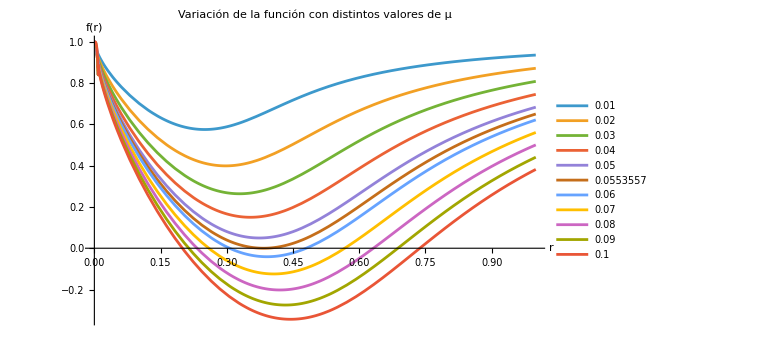

```mathematica
Plot[Evaluate@Table[f,{μ,{0.01,0.02,0.03,0.04,0.05,0.0553557367611073,0.06,0.07,0.08,0.09,0.1}}],{r2,0,1},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.01","0.02","0.03","0.04","0.05","0.0553557","0.06","0.07","0.08","0.09","0.1"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
```

### Casos fuera del constraint

Un caso especial b=1/16

```mathematica
b:=1/16
α:=0.5
Simplify[E1rees]
Simplify[B1rees]
Simplify[D1rees]
Simplify[D2rees]
Simplify[C1rees]
Clear[b,α]
```

0.5

-0.000312518

-0.000204591

0.233111-0.00762922 ⅈ

-0.0113507 r2^2 (1. r2^4-(1.44+2.69399 ⅈ) μ2-1.8854 √(0.28125 r2^8-(0.810185+1.51572 ⅈ) r2^4 μ2-(1.45833-2.18263 ⅈ) μ2^2))

Un caso interesante b=7/144. Es un caso trivial ya que la función no depende de μ

```mathematica
b:=7/144
Simplify[E1rees]
Simplify[B1rees]
Simplify[D1rees]
Assuming[α>0&&r2>0,FullSimplify[D2rees]]
Simplify[C1rees]
Assuming[α>0&&r2>0,FullSimplify[f3rees]]
Clear[b,α]
```

0

-(49 α^3)/8

-7/8 √21 α^3

-7/4 7^(2/3) (-1+(-1)^(2/3)) α^2

-49/512 r2^6 α^6

1+(3 r2^2)/2

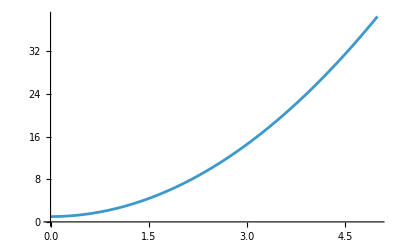

```mathematica
Plot[1+(3 r2^2)/2,{r2,0,5}]
```

Otro caso, bueno para analizar es b=7/162

```mathematica
b:=7/162
Simplify[E1rees]
Simplify[B1rees]
Simplify[D1rees]
Assuming[α>0&&r2>0,FullSimplify[D2rees]]
Simplify[C1rees]
Assuming[α>0&&r2>0,FullSimplify[f3rees]]
Clear[b,α]
```

-(7 α^2)/9

(49 ⅈ α^3)/(3 √3)

7/3 ⅈ √7 α^3

-7/3 (-7)^(2/3) α^2

-(392 r2^2 α^5 (9 (-1)^(2/3) α μ2-√3 (-1+(-1)^(1/3)) √(-α^2 (r2^8-27 μ2^2))))/(6561 (-1+(-1)^(1/3)))

1+r2^2+r2^(10/3)/(√3 (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))+(r2^(2/3) (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))/(√3)

```mathematica
FullSimplify[Series[1+r2^2+r2^(10/3)/(√3 (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))+(r2^(2/3) (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))/(√3),{r2,Infinity,2}]]
```

((3 r2^(8/3)+√3 r2^(4/3) (ⅈ r2^4)^(1/3)-ⅈ √3 (ⅈ r2^4)^(2/3)) r2^2)/(3 r2^(8/3))+1+((ⅈ r2^4)^(2/3) (-r2^(8/3)+(ⅈ r2^4)^(2/3)) μ2)/(r2^(16/3) r2^2)+O[1/r2]^(7/3)

```mathematica
Assuming[μ2>0&&r2>0,FullSimplify[Series[1+r2^2+r2^(10/3)/(√3 (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))+(r2^(2/3) (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))/(√3),{r2,0,2}]]]
```

1+μ2^(1/3)  r2^(2/3)+r2^2+O[r2]^(7/3)

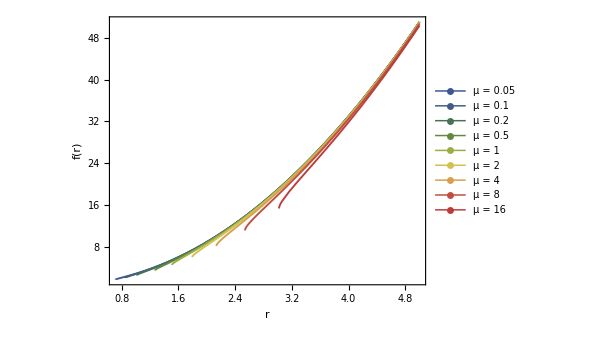

```mathematica
ClearAll[α,b];

α:=0.03;
b:=7/162;

muVals={0.05,0.1,0.2,0.5,1,2,4,8,16};

paperPlot=Plot[Evaluate@Table[f3rees,{μ2,muVals}],{r2,0,5},(*Estilo general*)PlotRange->All,MaxRecursion->6,ImageSize->450,AspectRatio->0.75,(*Líneas*)PlotStyle->Table[{Thickness[0.003],ColorData["DarkRainbow"][i]},{i,0,1,1/(Length[muVals]-1)}],(*Marco tipo paper*)Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.002]],(*Etiquetas*)FrameLabel->{Style["r",18,FontFamily->"Times"],Style["f(r)",18,FontFamily->"Times"]},(*Ticks*)FrameTicksStyle->Directive[14,FontFamily->"Times"],(*Leyenda*)PlotLegends->Placed[LineLegend[Table[Style[Row[{"μ = ",mu}],14,FontFamily->"Times"],{mu,muVals}],LegendMarkers->"",Spacings->0.8],Right]];

paperPlot

Clear[α,b];
```

```mathematica
Export["Casob7162.png",paperPlot]
```

Casob7162.png

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

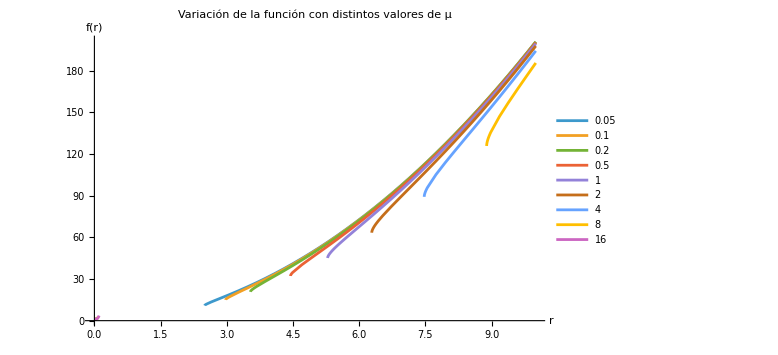

```mathematica
α:=0.03
Plot[Evaluate@Table[1+r2^2+(2^(1/3) (r2^10 α)^(1/3))/(√3 (-27 √3 μ+√(-4 r2^8 α^2+2187 μ^2))^(1/3))+(r2^(2/3) ((-27 √3 μ+√(-4 r2^8 α^2+2187 μ^2))/α)^(1/3))/(2^(1/3) √3),{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,10},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

```mathematica
f[r2_]:=1+r2^2+r2^(10/3)/(√3 (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))+(r2^(2/3) (-3 √3 μ2+√(-r2^8+27 μ2^2))^(1/3))/(√3)
Assuming[μ2>0&&r2>0,Series[Simplify[(12-24 f[r2]+12 f[r2]^2+6 r2^2 f'[r2]^2+r^4 f''[r2]^2)/r2^4],{r2,0,2}]]
```

-(4 ((-1)^(1/3) 2^(2/3) r^4 μ2^(2/3)))/(81 r2^(20/3))+(8 (-1)^(2/3) 2^(1/3) r^4 μ2^(1/3))/(9 r2^(16/3))+(4 r^4 (729+6 (-1)^(2/3) 2^(1/3) (18 2^(2/3) (-1/μ2)^(1/3)-(-1/2)^(1/3)/μ2^(1/3)) μ2^(1/3)))/(729 r2^4)+(8/27 r^4 (18 2^(2/3) (-1/μ2)^(1/3)-(-1/2)^(1/3)/μ2^(1/3))-44/3 (-1)^(1/3) 2^(2/3) μ2^(2/3))/r2^(8/3)+(4/729 r^4 (18 2^(2/3) (-1/μ2)^(1/3)-(-1/2)^(1/3)/μ2^(1/3))^2-40 (-1)^(2/3) 2^(1/3) μ2^(1/3))/r2^(4/3)+(20+8/27 (81-6 (-1)^(2/3) 2^(1/3) (2 2^(2/3) (-1/μ2)^(1/3)+(-1/2)^(1/3)/μ2^(1/3)) μ2^(1/3)))+(16/3 (2 2^(2/3) (-1/μ2)^(1/3)+(-1/2)^(1/3)/μ2^(1/3))+(4 (-1)^(1/3) 2^(2/3))/μ2^(1/3)+8/243 (-1)^(2/3) 2^(1/3) r^4 μ2^(1/3) (82 (((-1)^(2/3) 2^(1/3))/(9 μ2^(5/3))-(2 2^(1/3) ⅇ^((2 ⅈ π)/3))/(27 μ2^(5/3)))+(35 ⅇ^((2 ⅈ π)/3))/(54 2^(2/3) μ2^(5/3))+8 ((14 (-1)^(2/3) 2^(1/3))/(9 μ2^(5/3))+36 (-(2 (-1)^(2/3) 2^(1/3))/(27 μ2^(8/3))+(7 2^(1/3) ⅇ^((2 ⅈ π)/3))/(243 μ2^(8/3))) μ2))) r2^(4/3)+O[r2]^(7/3)

```mathematica
1/(r2^4 NN[r2]^2)(9 r2^4 f'[r2]^2 NN'[r2]^2+6 r2^4 NN[r2] f'[r2] NN'[r2] f''[r2]+NN[r2]^2 (12-24 f[r2]+12 f[r2]^2+6 r2^2 f'[r2]^2+r^4 f''[r2]^2)+12 r2^4 f[r2] f'[r2] NN'[r2] NN''[r2]+4 f[r2] NN[r] (3 r2^2 f'[r2] NN'[r2]+r2^4 f''[r2] NN''[r2])+4 f[r2]^2 (3 r2^2 NN'[r2]^2+r2^4 NN''[r2]^2))/.NN[r2]->1
```

(12-24 f[r2]+12 f[r2]^2+6 r2^2 f'[r2]^2+r^4 f''[r2]^2)/r2^4

### Expansión de la función reescalada y Constraint

```mathematica
Assuming[α>0&&μ2>0&&b>0&&r2>0,Simplify[Series[f3rees,{r2,Infinity,2}]]]
```

(1+(7-108 b)/(7^(1/3) (49+54 b (-21+√21 √(-7+144 b)))^(1/3))+(49+54 b (-21+√21 √(-7+144 b)))^(1/3)/7^(2/3)) r2^2+1-μ2/r2^2+O[1/r2]^(7/3)

```mathematica
Assuming[α>0&&μ2>0&&b>0&&r2>0,Simplify[Series[f3rees,{r2,0,2}]]]
```

1+1/2^(1/3)3 ((((1944 b^2 (4 √3 7^(1/6) (49+54 b (-21+√21 √(-7+144 b)))^(1/3)+63 √3 √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))-9 √7 √(-7+144 b) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))+7 (7^(2/3) √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(1/3)+49 √3 √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))-√3 7^(2/3) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))+54 b (-7 √3 7^(1/6) (49+54 b (-21+√21 √(-7+144 b)))^(1/3)-3 7^(2/3) √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(1/3)-245 √3 √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))+21 √7 √(-7+144 b) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))+3 √3 7^(2/3) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))-3 7^(1/6) √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) √(((-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(2/3) (343+1259712 b^3+756 b (-21+√21 √(-7+144 b))-17496 b^2 (-7+√21 √(-7+144 b))))/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))) μ)/((-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)) α)))^(1/3) r2^(2/3)+r2^2+O[r2]^(7/3)

```mathematica
Solve[1+(7-108 b)/(7^(1/3) (49+54 b (-21+√21 √(-7+144 b)))^(1/3))+(49+54 b (-21+√21 √(-7+144 b)))^(1/3)/7^(2/3)==0,b]
```

{{}}

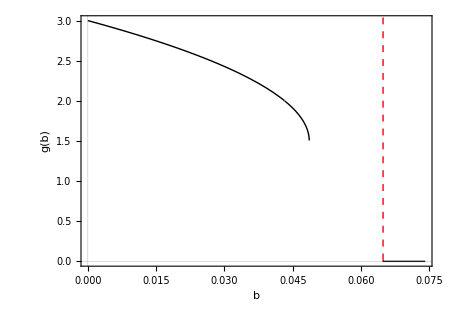

```mathematica
figb1=Plot[1+(7-108 b)/(7^(1/3) (49+54 b (-21+Sqrt[21] Sqrt[-7+144 b]))^(1/3))+(49+54 b (-21+Sqrt[21] Sqrt[-7+144 b]))^(1/3)/7^(2/3),{b,0,8/108},PlotRange->All,PlotStyle->{Black,Thick},Frame->True,Axes->False,FrameLabel->{Style["b",16,FontFamily->"Times"],Style["g(b)",16,FontFamily->"Times"]},FrameTicks->{Automatic,Automatic},LabelStyle->Directive[14,FontFamily->"Times"],ImageSize->450,AspectRatio->0.7,PlotTheme->"Scientific",Epilog->{{Red,Dashed,Thick,InfiniteLine[{{7/108,0},{7/108,1}}]},Text[Style["b = 7/108",14,Red,FontFamily->"Times"],{-1,0}]}]
```

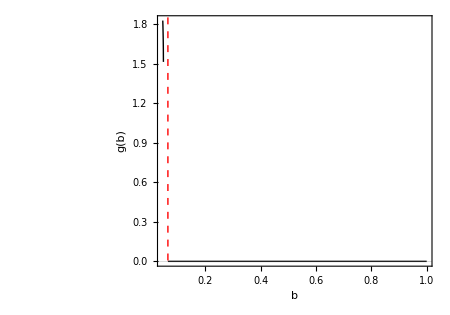

```mathematica
figb2=Plot[1+(7-108 b)/(7^(1/3) (49+54 b (-21+Sqrt[21] Sqrt[-7+144 b]))^(1/3))+(49+54 b (-21+Sqrt[21] Sqrt[-7+144 b]))^(1/3)/7^(2/3),{b,5/108,1},PlotRange->All,PlotStyle->{Black,Thick},Frame->True,Axes->False,FrameLabel->{Style["b",16,FontFamily->"Times"],Style["g(b)",16,FontFamily->"Times"]},FrameTicks->{Automatic,Automatic},LabelStyle->Directive[14,FontFamily->"Times"],ImageSize->450,AspectRatio->0.7,PlotTheme->"Scientific",Epilog->{{Red,Dashed,Thick,InfiniteLine[{{7/108,0},{7/108,1}}]},Text[Style["b = 7/108",14,Red,FontFamily->"Times"],{-1,0}]}]
```

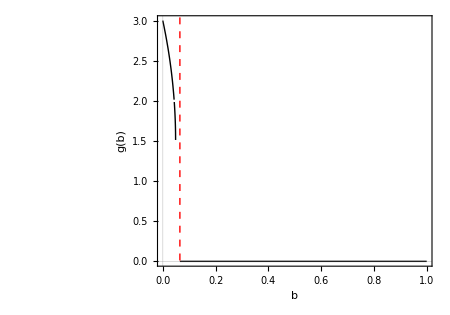

```mathematica
figb3=Plot[1+(7-108 b)/(7^(1/3) (49+54 b (-21+Sqrt[21] Sqrt[-7+144 b]))^(1/3))+(49+54 b (-21+Sqrt[21] Sqrt[-7+144 b]))^(1/3)/7^(2/3),{b,0,1},PlotRange->All,PlotStyle->{Black,Thick},Frame->True,Axes->False,FrameLabel->{Style["b",16,FontFamily->"Times"],Style["g(b)",16,FontFamily->"Times"]},LabelStyle->Directive[14,FontFamily->"Times"],ImageSize->450,AspectRatio->0.7,PlotTheme->"Scientific",Epilog->{{Red,Dashed,Thick,InfiniteLine[{{7/108,0},{7/108,1}}]},Text[Style["b = 7/108",14,Red,FontFamily->"Times"],{-1,0}]}]
```

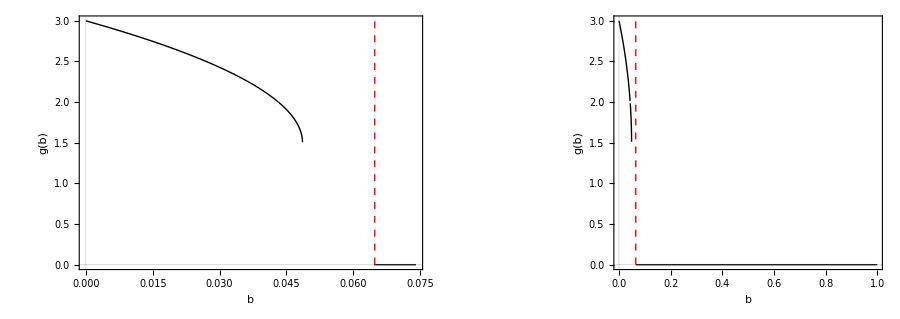

```mathematica
figb=GraphicsRow[{figb1,figb3},ImageSize->900,Spacings->20]
```

```mathematica
Export["Constraint b.png",figb]
```

Constraint b.png

### Otro reescalado β=l^2 α

```mathematica
f3rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&l>0,Simplify[f3sim/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
```

1+r2^2+(36 l^2 r2^4 (-108 l^2+7 α))/(7 (-46656/7 l^6 r2^6 (162 l^2-7 α) α^2+(629856 l^6 r2^2 α^2 √((144 l^2-7 α) α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (-108 7^(2/3) l^2 α+7 7^(2/3) α^2-7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+69984/7 l^6 r2^2 α √(3888/7 l^4 r2^8 (144 l^2-7 α) α-(84 r2^4 α^2 √((144 l^2-7 α) α) (-162 l^2+7 α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+(3969 (144 l^2-7 α) α^3 (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(8/3) μ^2)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α)))^2 (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3))^2)))^(1/3))+1/(36 l^2 α)(-46656/7 l^6 r2^6 (162 l^2-7 α) α^2+(629856 l^6 r2^2 α^2 √((144 l^2-7 α) α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (-108 7^(2/3) l^2 α+7 7^(2/3) α^2-7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+69984/7 l^6 r2^2 α √(3888/7 l^4 r2^8 (144 l^2-7 α) α-(84 r2^4 α^2 √((144 l^2-7 α) α) (-162 l^2+7 α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+(3969 (144 l^2-7 α) α^3 (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(8/3) μ^2)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α)))^2 (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3))^2)))^(1/3)

```mathematica
E1rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[E1/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
B1rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[B1/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
D1rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[D1/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
D2rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[D2/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
C1rees2=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[C1/.β->l^2*α/.r->Sqrt[36/7]l*r2]]
```

(144 l^2-7 α) α

49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α))

7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))

-108 7^(2/3) l^2 α+7 7^(2/3) α^2-7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)

-46656/49 l^6 r2^6 (162 l^2-7 α) α^2+(629856 l^6 r2^2 α^2 √((144 l^2-7 α) α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/(7 (7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (-108 7^(2/3) l^2 α+7 7^(2/3) α^2-7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+69984/49 √(3/7) l^4 r2^2 α √(l^4 (1296 l^4 r2^8 (144 l^2-7 α) α-(196 r2^4 α^2 √((144 l^2-7 α) α) (-162 l^2+7 α) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(4/3) μ)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α))) (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3)))+(9261 (144 l^2-7 α) α^3 (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(8/3) μ^2)/((7 √21 α^3+162 l^2 α (-√21 α+√((144 l^2-7 α) α)))^2 (108 7^(2/3) l^2 α-7 7^(2/3) α^2+7^(1/3) (49 α^3+54 l^2 α (-21 α+√21 √((144 l^2-7 α) α)))^(2/3))^2)))

### Casos dentro del constraint

Variamos α y b

#### α=0.005 y b=8/108

1+r2^2-(9.52381×10^-6 r2^4)/((-2.1164×10^-13 r2^6-2.66667×10^-10 r2^2 μ+1.79583×10^-10 r2^2 √(1.39683×10^-6 r2^8+0.0035 r2^4 μ+2.205 μ^2))^(1/3))+15000. (-2.1164×10^-13 r2^6-2.66667×10^-10 r2^2 μ+1.79583×10^-10 r2^2 √(1.39683×10^-6 r2^8+0.0035 r2^4 μ+2.205 μ^2))^(1/3)

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

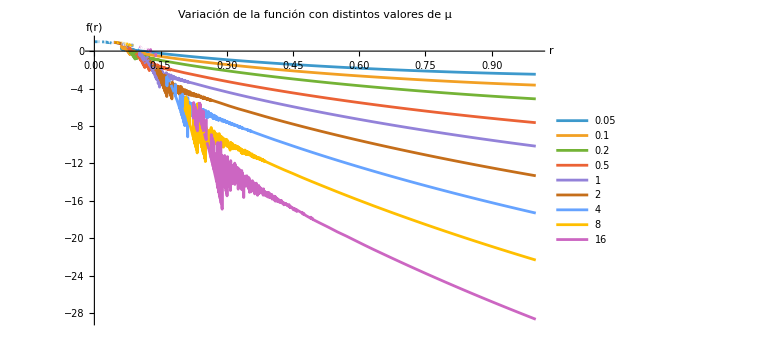

```mathematica
α:=0.005
b:=8/108
f3rees
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,1},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=1/16

```mathematica
α:=0.0005
b:=1/16
f3rees
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

1+r2^2+(2.00893×10^-8 r2^4)/((-7.94547×10^-20 r2^6+(7.11914×10^-16+1.33187×10^-15 ⅈ) r2^2 μ+3.41119×10^-15 r2^2 √(5.42411×10^-10 r2^8-(9.72222×10^-6+0.0000181886 ⅈ) r2^4 μ-(0.108889-0.16297 ⅈ) μ^2))^(1/3))+1.77778×10^6 (-7.94547×10^-20 r2^6+(7.11914×10^-16+1.33187×10^-15 ⅈ) r2^2 μ+3.41119×10^-15 r2^2 √(5.42411×10^-10 r2^8-(9.72222×10^-6+0.0000181886 ⅈ) r2^4 μ-(0.108889-0.16297 ⅈ) μ^2))^(1/3)

-Graphics-

#### α=0.005 y b=1/2

1+r2^2-(0.00302143 r2^4)/((-9.63321×10^-10 r2^6-8.20125×10^-8 r2^2 μ+5.52301×10^-8 r2^2 √(0.00112821 r2^8+0.0518 r2^4 μ+2.205 μ^2))^(1/3))+2222.22 (-9.63321×10^-10 r2^6-8.20125×10^-8 r2^2 μ+5.52301×10^-8 r2^2 √(0.00112821 r2^8+0.0518 r2^4 μ+2.205 μ^2))^(1/3)

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

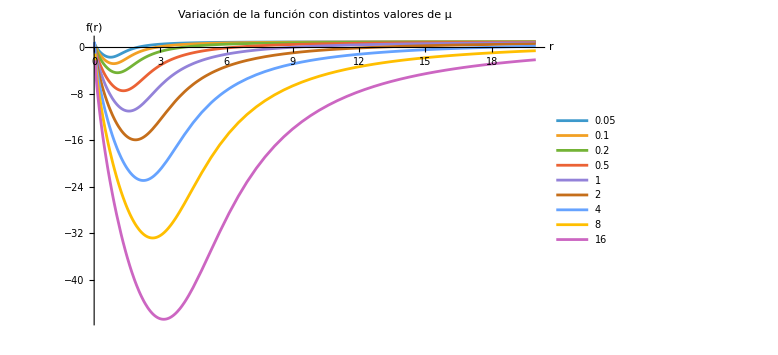

```mathematica
α:=0.005
b:=1/2
f3rees
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.03 y b=1

```mathematica
f3rees1[r,1,0.03,μ]
```

1+r^2+1/7^(2/3)r^(2/3) (-1085 r^4+(486 7^(2/3) √137 (49+54 (-21+√2877))^(4/3) μ)/((-7 √21+162 (√21-√137)) (101 7^(1/3)+(49+54 (-21+√2877))^(2/3)))+2749.55 √(1.1097 r^8+0.3255 r^4 μ+0.1701 μ^2))^(1/3)-(101 r^(10/3))/(-7595 r^4+(3402 7^(2/3) √137 (49+54 (-21+√2877))^(4/3) μ)/((-7 √21+162 (√21-√137)) (101 7^(1/3)+(49+54 (-21+√2877))^(2/3)))+19246.8 √(1.1097 r^8+0.3255 r^4 μ+0.1701 μ^2))^(1/3)

1+r2^2+1/7^(2/3)r2^(2/3) (-1085 r2^4+(486 7^(2/3) √137 (49+54 (-21+√2877))^(4/3) μ2)/((-7 √21+162 (√21-√137)) (101 7^(1/3)+(49+54 (-21+√2877))^(2/3)))+2749.55 √(1.1097 r2^8+0.3255 r2^4 μ2+0.1701 μ2^2))^(1/3)-(101 r2^(10/3))/(-7595 r2^4+(3402 7^(2/3) √137 (49+54 (-21+√2877))^(4/3) μ2)/((-7 √21+162 (√21-√137)) (101 7^(1/3)+(49+54 (-21+√2877))^(2/3)))+19246.8 √(1.1097 r2^8+0.3255 r2^4 μ2+0.1701 μ2^2))^(1/3)

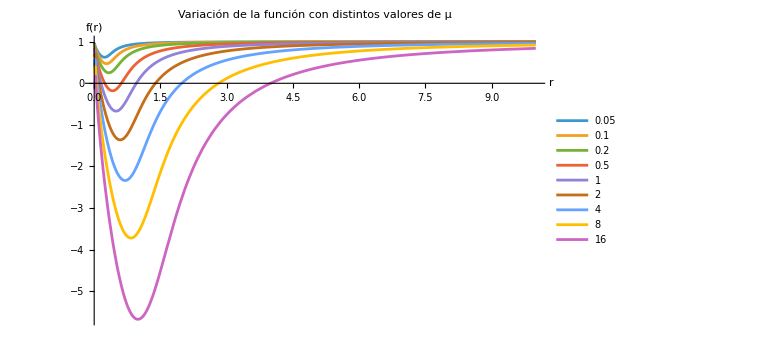

```mathematica
α:=0.03
b:=1
f3rees
Plot[Evaluate@Table[f3rees,{μ2,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,10},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=2

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

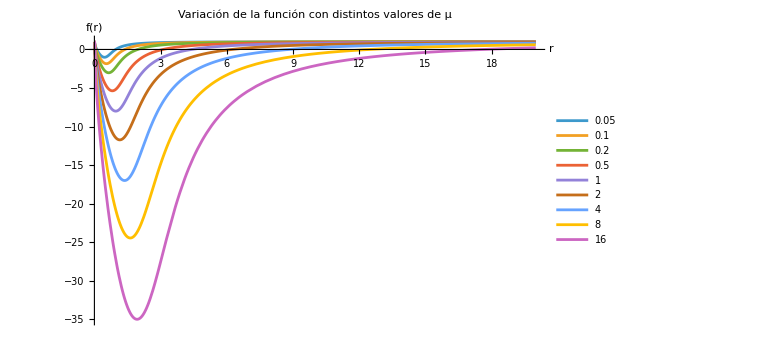

```mathematica
α:=0.005
b:=2
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=4

Power::infy: Infinite expression 1/0.^(1/3) encountered.

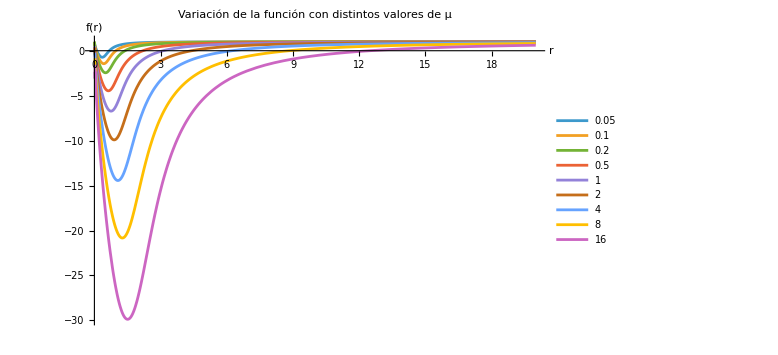

```mathematica
α:=0.005
b:=4
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=16

Power::infy: Infinite expression 1/0.^(1/3) encountered.

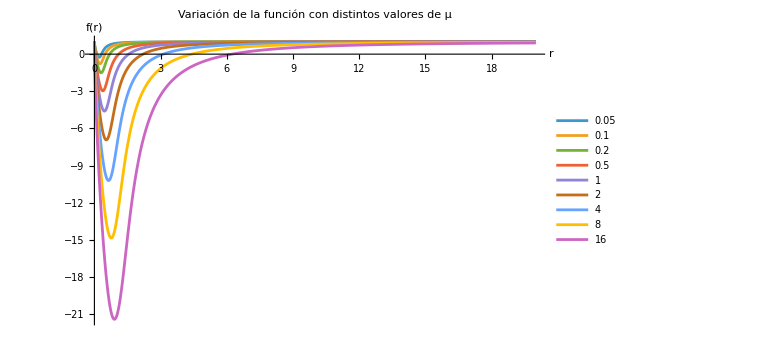

```mathematica
α:=0.005
b:=16
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.01 y b=8/108

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

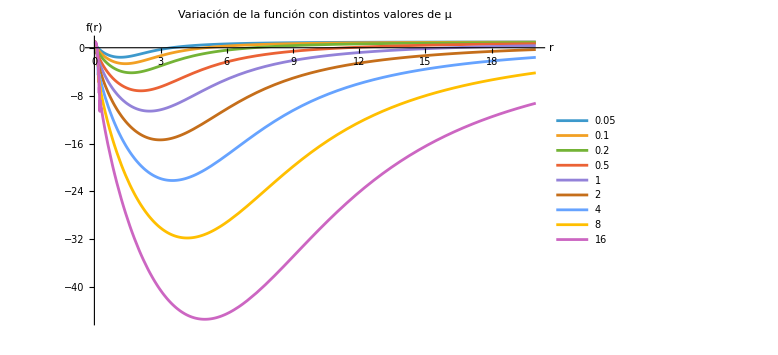

```mathematica
α:=0.01
b:=8/108
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

### Agujero regular típico

```mathematica
ft[r_,μ_]=Simplify[f3rees1[r,1/8,4,μ]]
```

1+r^2+1/7^(2/3)r^(2/3) (-(371 r^4)/4-(243 7^(2/3) √11 (-371+27 √231)^(4/3) μ)/(2^(2/3) (81 √11-53 √21) (26 7^(1/3)+(-742+54 √231)^(2/3)))+9/4 √(2079 r^8+(31164 7^(1/6) (297 √3-53 √77) (-742+54 √231)^(1/3) r^4 μ)/((81 √11-53 √21) (26 7^(1/3)+(-742+54 √231)^(2/3)))+(523908 7^(1/3) (-742+54 √231)^(2/3) μ^2)/((26 7^(1/3)+(-742+54 √231)^(2/3))^2)))^(1/3)-(13 r^(10/3))/(2 (-(2597 r^4)/4-(1701 7^(2/3) √11 (-371+27 √231)^(4/3) μ)/(2^(2/3) (81 √11-53 √21) (26 7^(1/3)+(-742+54 √231)^(2/3)))+63/4 √(2079 r^8+(31164 7^(1/6) (297 √3-53 √77) (-742+54 √231)^(1/3) r^4 μ)/((81 √11-53 √21) (26 7^(1/3)+(-742+54 √231)^(2/3)))+(523908 7^(1/3) (-742+54 √231)^(2/3) μ^2)/((26 7^(1/3)+(-742+54 √231)^(2/3))^2)))^(1/3))

```mathematica
Simplify[Series[ft[r,μ],{r,Infinity,2}]]
```

Series::ztest1: Unable to decide whether numeric quantity 1+(-371+27 √231)^(1/3)/14^(2/3)-13/(14 (-371+27 √231))^(1/3) is equal to zero. Assuming it is.

1-(2 (2^(2/3) (-330561+21860 √231) (13 14^(1/3)+(-371+27 √231)^(2/3)) μ))/((√11 (81 √11-53 √21) (-371+27 √231) (26 7^(1/3)+(-742+54 √231)^(2/3))) r^2)+O[1/r]^(7/3)

```mathematica
Simplify[Series[ft[r,μ],{r,0,2}]]
```

1+(3 3^(2/3) 11^(1/6) (-371+27 √231)^(1/9) (-((53 √7-27 √33) (-μ+√(μ^2))))^(1/3) r^(2/3))/(2^(2/9) 7^(5/18) ((81 √11-53 √21) (26 7^(1/3)+(-742+54 √231)^(2/3)))^(1/3))+r^2+O[r]^(8/3)

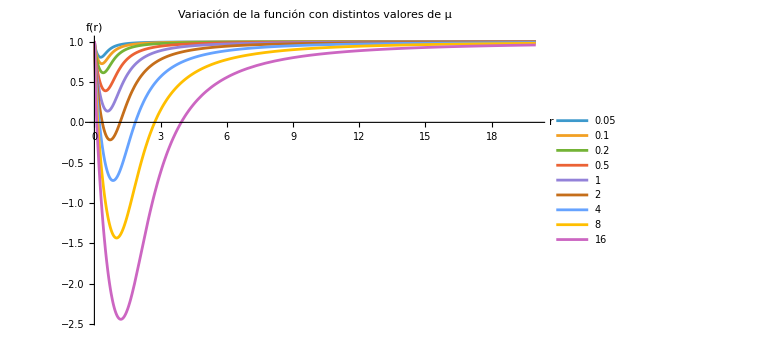

```mathematica
Plot[Evaluate@Table[ft[r,μ],{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

```mathematica
N[1/16]
```

0.0625

### Invariante de Kretschman

```mathematica
NN[r2_]:=1
b:=1
α:=1
f[r2_]:=f3rees
Krt[r2_]=Assuming[r2>0&&μ>0&&α>0&&b>0,Simplify[1/(r2^4 NN[r2]^2)(9 r2^4 f'[r2]^2 NN'[r2]^2+6 r2^4 NN[r2] f'[r2] NN'[r2] f''[r2]+NN[r2]^2 (12-24 f[r2]+12 f[r2]^2+6 r2^2 f'[r2]^2+r^4 f''[r2]^2)+12 r2^4 f[r2] f'[r2] NN'[r2] NN''[r2]+4 f[r2] NN[r] (3 r2^2 f'[r2] NN'[r2]+r2^4 f''[r2] NN''[r2])+4 f[r2]^2 (3 r2^2 NN'[r2]^2+r2^4 NN''[r2]^2))]]
```

(12 (-1+f3rees)^2)/r2^4